```mathematica
SetDirectory[NotebookDirectory[]];
```

## Dynamical Activity

```mathematica
x = Transpose[Import["A1/act.dat"]];
```

```mathematica
Nstretch =10; 
Nstretchneurons = 4;
Nunits = 10;
Nunitneurons = 6;
Nmuscles = 24;
Nactmuscles = 2;
```

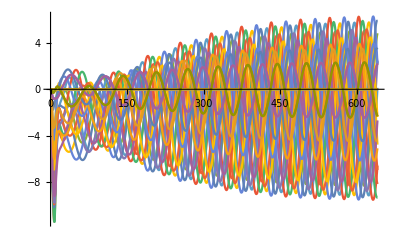

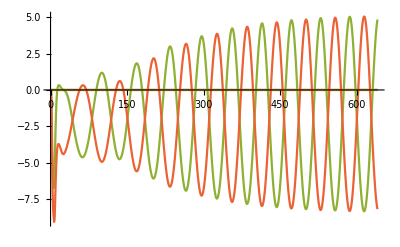

```mathematica
ListLinePlot[Take[x,{2,Nstretch Nstretchneurons+1}],PlotRange->All]
ListLinePlot[Take[x,{2, Nstretchneurons+1}],PlotRange->All]
```

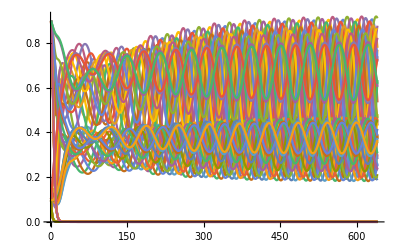

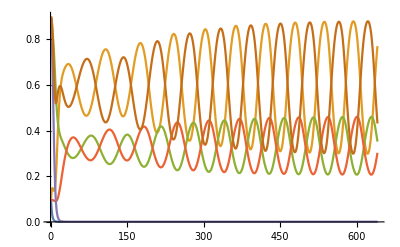

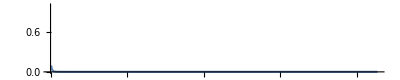

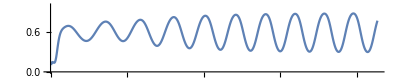

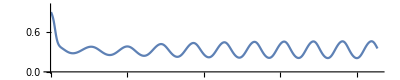

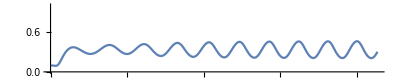

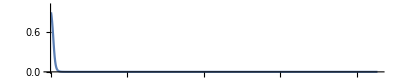

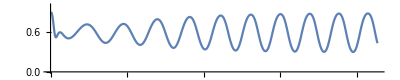

```mathematica
ListLinePlot[Take[x,{Nstretch Nstretchneurons+2,Nstretch Nstretchneurons+Nunits Nunitneurons + 1}],PlotRange->All]
ListLinePlot[Take[x,{Nstretch Nstretchneurons+2,Nstretch Nstretchneurons+ Nunitneurons + 1}],PlotRange->All]
ListLinePlot[Take[x,{Nstretch Nstretchneurons+2,Nstretch Nstretchneurons+ 2}],AspectRatio->1/5,PlotRange->{All,{0,1}}]
ListLinePlot[Take[x,{Nstretch Nstretchneurons+3,Nstretch Nstretchneurons+ 3}],AspectRatio->1/5,PlotRange->{All,{0,1}}]
ListLinePlot[Take[x,{Nstretch Nstretchneurons+4,Nstretch Nstretchneurons+ 4}],AspectRatio->1/5,PlotRange->{All,{0,1}}]
ListLinePlot[Take[x,{Nstretch Nstretchneurons+5,Nstretch Nstretchneurons+ 5}],AspectRatio->1/5,PlotRange->{All,{0,1}}]
ListLinePlot[Take[x,{Nstretch Nstretchneurons+6,Nstretch Nstretchneurons+ 6}],AspectRatio->1/5,PlotRange->{All,{0,1}}]
ListLinePlot[Take[x,{Nstretch Nstretchneurons+7,Nstretch Nstretchneurons+ 7}],AspectRatio->1/5,PlotRange->{All,{0,1}}]
```

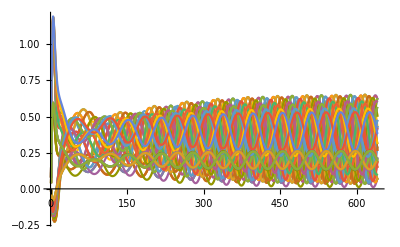

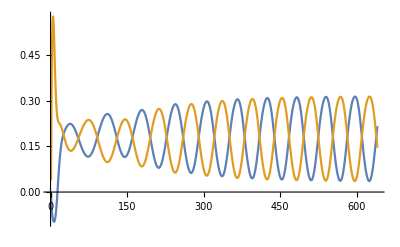

```mathematica
ListLinePlot[Take[x,{Nstretch Nstretchneurons+Nunits Nunitneurons + 2,Nstretch Nstretchneurons+Nunits Nunitneurons+Nmuscles Nactmuscles+1}],PlotRange->All]
ListLinePlot[Take[x,{Nstretch Nstretchneurons+Nunits Nunitneurons + 2,Nstretch Nstretchneurons+Nunits Nunitneurons+ Nactmuscles+1}],PlotRange->All]
```

## Behavior

```mathematica
cd=ColorData[97,"ColorList"];
```

### Definitions

```mathematica
Needs["Notation`"];
```

```mathematica
Subscript[N, Segments]=50               (* Number of segments *);
Subscript[R, Min]=40.0×10^-6       (* Minor radius of prolate ellipse body in m *);
Subscript[L, worm]=1.0×10^-3       (* Length of worm in m *);
```

```mathematica
R[i_]:=Subscript[R, Min] Abs[Sin[ArcCos[(i-(Subscript[N, Segments]/2+1))/(Subscript[N, Segments]/2+0.2)]]]
```

```mathematica
(* Display the worm model given a vector of segment state vectors *)

DisplayWormModelB[Ss_,Color_,opts:OptionsPattern[Graphics]]:=
Module[{AllPDs,HeadPDs, VNC1PDs,OtherPDs,AllPVs,HeadPVs,VNC1PVs,OtherPVs},
AllPDs=Table[{Ss⟦i,1⟧+R[i]Cos[Ss⟦i,3⟧],Ss⟦i,2⟧+R[i]Sin[Ss⟦i,3⟧]},{i,1,Subscript[N, Segments]+1}];
HeadPDs=Table[{Ss⟦i,1⟧+R[i]Cos[Ss⟦i,3⟧],Ss⟦i,2⟧+R[i]Sin[Ss⟦i,3⟧]},{i,1,8}];
VNC1PDs=Table[{Ss⟦i,1⟧+R[i]Cos[Ss⟦i,3⟧],Ss⟦i,2⟧+R[i]Sin[Ss⟦i,3⟧]},{i,9,16}];OtherPDs=Table[{Ss⟦i,1⟧+R[i]Cos[Ss⟦i,3⟧],Ss⟦i,2⟧+R[i]Sin[Ss⟦i,3⟧]},{i,17,Subscript[N, Segments]+1}];
AllPVs=Table[{Ss⟦i,1⟧-R[i]Cos[Ss⟦i,3⟧],Ss⟦i,2⟧-R[i]Sin[Ss⟦i,3⟧]},{i,1,Subscript[N, Segments]+1}];
HeadPVs=Table[{Ss⟦i,1⟧-R[i]Cos[Ss⟦i,3⟧],Ss⟦i,2⟧-R[i]Sin[Ss⟦i,3⟧]},{i,1,8}];
VNC1PVs=Table[{Ss⟦i,1⟧-R[i]Cos[Ss⟦i,3⟧],Ss⟦i,2⟧-R[i]Sin[Ss⟦i,3⟧]},{i,9,16}];
OtherPVs=Table[{Ss⟦i,1⟧-R[i]Cos[Ss⟦i,3⟧],Ss⟦i,2⟧-R[i]Sin[Ss⟦i,3⟧]},{i,17,Subscript[N, Segments]+1}];
Graphics[
{Gray,Thickness[0.003],MapThread[Line[{#1,#2}]&,{AllPDs,AllPVs}],
LightGray,Thickness[0.002],MapThread[Line[{#1,#2}]&,{Drop[AllPDs,-1],Drop[AllPVs,1]}],MapThread[Line[{#1,#2}]&,{Drop[AllPDs,1],Drop[AllPVs,-1]}],
cd[[1]],Thickness[0.002],Line[HeadPDs],cd[[2]],Thickness[0.002],Line[HeadPVs],
cd[[3]],Thickness[0.002],Line[VNC1PDs],cd[[4]],Thickness[0.002],Line[VNC1PVs],
Gray,Thickness[0.002],Line[OtherPDs],Gray,Thickness[0.002],Line[OtherPVs]
(*,LightGray,PointSize[0.004],Map[Point,Join[PDs,PVs]]*)
},
opts]]
```

### Agar

```mathematica
data=Import["A1/body.dat"];
```

```mathematica
w=0.002;
```

```mathematica
Manipulate[
Show[
DisplayWormModelB[Partition[Rest[data⟦t⟧],3],Gray],
Axes->False,PlotRange->{{-3w/2,w/2},{-w/3,w/3}},AspectRatio->1/3,ImageSize->700
],
{t,1,Length[data],1}]
```

Part::partd: Part specification data⟦378⟧ is longer than depth of object.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Show::gtype: DisplayWormModelB is not a type of graphics.

## Fitness Maps (Coarse ~11min)

make clean; make; mv main fitnessmap; time ./fitnessmap

### Slice 1: Cross-connections: Excitatory Chemical Synapses intra-unit [9,10]

#### Coarse (0.5): 11 min

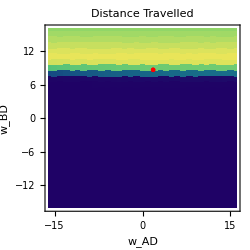

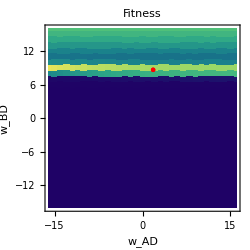

```mathematica
dA = Import["A1/distmap_1_9_10.dat"];
best ={{1.814995513,8.629590545}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"w_AD","w_BD"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_1_9_10.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"w_AD","w_BD"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

### Slice 2: Cross-connections: Inhibitory Chemical Synapses intra-unit [11,12]

#### Coarse (0.5): 11 min

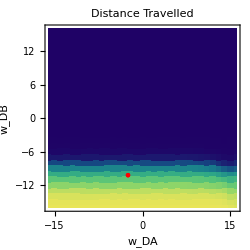

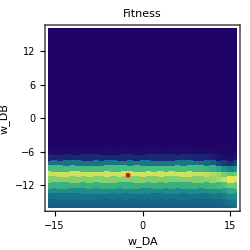

```mathematica
dA = Import["A1/distmap_1_11_12.dat"];
best ={{-2.471707785,-10.19050307}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"w_DA","w_DB"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_1_11_12.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"w_DA","w_DB"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

### Slice 3: Electrical Synapse Inter-segment connections [13,14]

#### Coarse (0.05): 11 min

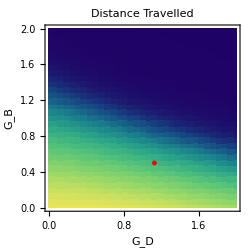

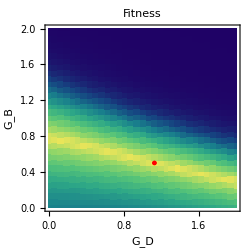

```mathematica
dA = Import["A1/distmap_0.06_13_14.dat"];
best = {{1.127118045,0.4992375944}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"G_D","G_B"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.06_13_14.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"G_D","G_B"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

### Slice 4: Excitatory VNC NMJ Weight [15,16]

#### Coarse (0.05): 11 min

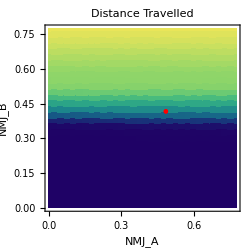

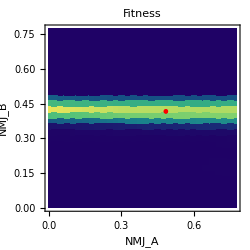

```mathematica
dA = Import["A1/distmap_0.025_15_16.dat"];
best = {{0.4841910927,0.4166470217}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"NMJ_A","NMJ_B"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.025_15_16.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"NMJ_A","NMJ_B"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

### Slice 5: Biases [4,5]

#### Coarse (0.5): 11 min

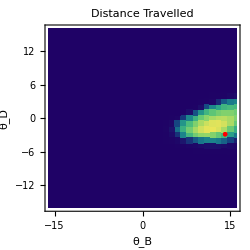

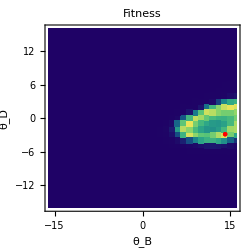

```mathematica
dA = Import["A1/distmap_1_4_5.dat"];
best = {{14.1019593,-2.874709794}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_B","θ_D"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_1_4_5.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_B","θ_D"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

### Slice 6: Self-Connections [7,8]

#### Coarse (0.5): 11 min

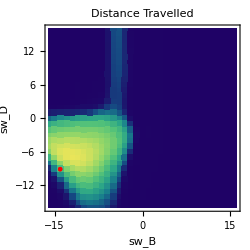

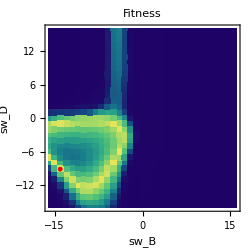

```mathematica
dA = Import["A1/distmap_1_7_8.dat"];
best ={{ -14.05465361,-9.118969497}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"sw_B","sw_D"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_1_7_8.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"sw_B","sw_D"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

### Slice 7: A neuron [3,6]

#### Coarse (0.5): 11 min

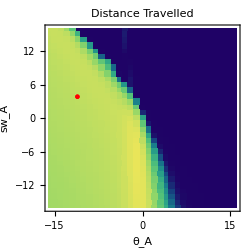

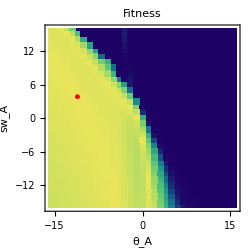

```mathematica
dA = Import["A1/distmap_1_3_6.dat"];
best = {{-11.10676509,3.827432716}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_A","sw_A"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_1_3_6.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0.0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_A","sw_A"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

### Slice 8: B neuron [4,7]

#### Coarse (0.5): 11 min

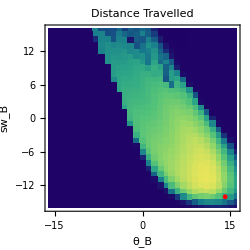

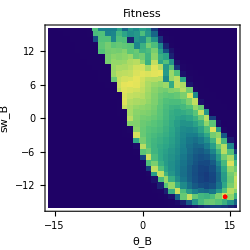

```mathematica
dA = Import["A1/distmap_1_4_7.dat"];
best = {{14.1019593,-14.05465361}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_B","sw_B"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_1_4_7.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0.0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_B","sw_B"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

### Slice 9: D neuron [5,8]

#### Coarse (1.0): 11 min

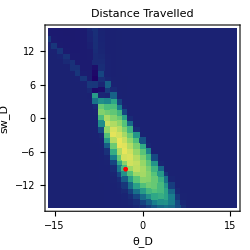

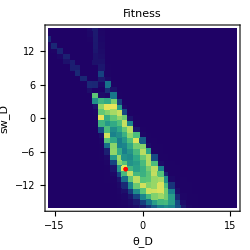

```mathematica
dA = Import["A1/distmap_1_5_8.dat"];
best = {{-2.874709794,-9.118969497 }};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_D","sw_D"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_1_5_8.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0.0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_D","sw_D"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

## Fitness Maps (Fine ~16hours)

make clean; make; mv main fitnessmap; time ./fitnessmap

### Slice 1: Cross-connections: Excitatory Chemical Synapses intra-unit [9,10]

#### Coarse (0.5): 11 min

```mathematica
dA = Import["A1/distmap_0.1_9_10.dat"];
best ={{1.814995513,8.629590545}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"w_AD","w_BD"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.1_9_10.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"w_AD","w_BD"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

-Graphics-

-Graphics-

### Slice 2: Cross-connections: Inhibitory Chemical Synapses intra-unit [11,12]

#### Coarse (0.5): 11 min

```mathematica
dA = Import["A1/distmap_0.1_11_12.dat"];
best ={{-2.471707785,-10.19050307}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"w_DA","w_DB"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.1_11_12.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"w_DA","w_DB"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

-Graphics-

-Graphics-

### Slice 3: Electrical Synapse Inter-segment connections [13,14]

#### Coarse (0.05): 11 min

```mathematica
dA = Import["A1/distmap_0.00625_13_14.dat"];
best = {{1.127118045,0.4992375944}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"G_D","G_B"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.00625_13_14.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"G_D","G_B"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

-Graphics-

-Graphics-

### Slice 4: Excitatory VNC NMJ Weight [15,16]

#### Coarse (0.05): 11 min

```mathematica
dA = Import["A1/distmap_0.0025_15_16.dat"];
best = {{0.4841910927,0.4166470217}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"NMJ_A","NMJ_B"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.0025_15_16.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"NMJ_A","NMJ_B"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

-Graphics-

-Graphics-

### Slice 5: Biases [4,5]

#### Coarse (0.5): 11 min

```mathematica
dA
```

{{-16,-16,2.29669×10^-8},{-16,-15.9,2.29517×10^-8},{-16,-15.8,2.29363×10^-8},{-16,-15.7,2.29208×10^-8},{-16,-15.6,2.29057×10^-8},103031,{16,15.6,2.1611×10^-7},{16,15.7,2.14625×10^-7},{16,15.8,2.13168×10^-7},{16,15.9,2.11741×10^-7},{16,16,2.10342×10^-7}}
 |  |  |  |

```mathematica
dA = Import["A1/distmap_0.1_4_5.dat"];
best = {{14.1019593,-2.874709794}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_B","θ_D"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.1_4_5.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_B","θ_D"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

-Graphics-

-Graphics-

### Slice 6: Self-Connections [7,8]

#### Coarse (0.5): 11 min

```mathematica
dA = Import["A1/distmap_0.1_7_8.dat"];
best ={{ -14.05465361,-9.118969497}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"sw_B","sw_D"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.1_7_8.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"sw_B","sw_D"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

-Graphics-

-Graphics-

### Slice 7: A neuron [3,6]

#### Coarse (0.5): 11 min

```mathematica
dA = Import["A1/distmap_0.1_3_6.dat"];
best = {{-11.10676509,3.827432716}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_A","sw_A"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.1_3_6.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0.0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_A","sw_A"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

-Graphics-

-Graphics-

### Slice 8: B neuron [4,7]

#### Coarse (0.5): 11 min

```mathematica
dA = Import["A1/distmap_0.1_4_7.dat"];
best = {{14.1019593,-14.05465361}};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_B","sw_B"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.1_4_7.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0.0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_B","sw_B"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

-Graphics-

-Graphics-

### Slice 9: D neuron [5,8]

#### Coarse (1.0): 11 min

```mathematica
dA = Import["A1/distmap_0.1_5_8.dat"];
best = {{-2.874709794,-9.118969497 }};
Show[
{
ListDensityPlot[dA,PlotRange->All,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_D","sw_D"},PlotLabel->"Distance Travelled",AspectRatio->1,ImageSize->250
]
fA = Import["A1/fitmap_0.1_5_8.dat"];
Show[
{
ListDensityPlot[fA,PlotRange->{{-16,16},{-16,16},{0.0,1}},InterpolationOrder->0,ColorFunction->"BlueGreenYellow"],
ListPlot[best,PlotStyle->Red]
},
PlotRange->All,Frame->True,FrameLabel->{"θ_D","sw_D"},PlotLabel->"Fitness",AspectRatio->1,ImageSize->250
]
```

-Graphics-

-Graphics-